# Prvi koraki v Mathematici

Avtor: Andrej Bauer
Priredila: Alen Orbanić, Matjaž Željko

## Kaj je Mathematica?

Mathematica je sistem za simbolno in numerično računanje. Mathematico je zasnoval Stephen Wolfram, danes pa jo razvija in prodaja njegovo podjetje Wolfram Research iz ZDA.

Mathematico si lahko predstavljamo kot zelo napreden kalkulator. Z njo lahko računamo:

```mathematica
2+2
```

4

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

Mathematica zna računati z natančnimi števili, se pravi, da ne zaokroži rezultatov, razen če to zahteva uporabnik:

```mathematica
Sin[Pi/3]
```

(√3)/2

```mathematica
Sin[Pi/5]
```

√(5/8-(√5)/8)

```mathematica
N[Sin[Pi/5]]
```

0.587785

```mathematica
N[Sin[Pi/5],42]
```

0.587785252292473129168705954639072768597652

Mathematica zna računati s simboli in ne samo s števili:

```mathematica
x+y+2 x-2 y+3 x
```

6 x-y

```mathematica
Factor[x^5 + x + 1]
```

(1+x+x^2) (1-x^2+x^3)

Izraze lahko vnašamo tudi v vizualno privlačnejši obliki. Za ta namen uporabimo menu Palletes.

```mathematica
Factor[x^5+x + 1]
```

(1+x+x^2) (1-x^2+x^3)

```mathematica
Simplify[Cos[4x]Cos[2x] Cos[x]  Sin[x]]
```

1/8 Sin[8 x]

Vendar zna Mathematica še veliko več. Na primer, računa odvode, integrale, lastne vrednosti, rešuje enačbe, riše grafe ...

```mathematica
D[f[x] g[x], x]
```

g[x] f'[x]+f[x] g'[x]

```mathematica
Integrate[x^2 Sin[x], x]
```

-(-2+x^2) Cos[x]+2 x Sin[x]

```mathematica
Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]
```

{3/2 (5+√33),3/2 (5-√33),0}

```mathematica
Solve[x^2==x+1,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

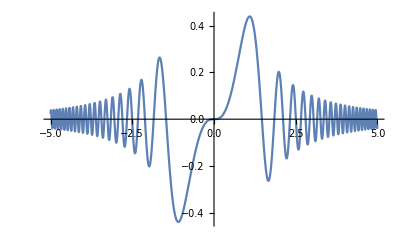

```mathematica
Plot[Sin[x^3]/(1+x^2),{x,-5,5},PlotRange->All]
```

```mathematica
Plot3D[Cos[√(x^2+y^2)]/Log[2+x^2+y^2],{x,-15,15},{y,-15,15},PlotPoints->70,PlotRange->All]
```

-Graphics3D-

Mathematica je močno orodje, ki ga lahko študentje s pridom uporabljajo pri svojem študiju, če se le potrudijo in se naučijo, kako sistem deluje in kako se ga uporablja. Dobljene rezultate lahko pretvorimo v matematični zapis v TeXu.

```mathematica
Integrate[(x+1)/(x^2+1),x] // TeXForm
```

\frac{1}{2} \log \left(x^2+1\right)+\tan ^{-1}(x)

## Uporabniški vmesnik in jedro

Mathematica je sestavljena iz dveh delov. Prvi je uporabniški vmesnik (frontend), v katerem urejamo dokumente, ki vsebujejo račune, besedilo in grafiko. Uporabniški vmestnik ničesar ne računa sam, ampak samo skrbi za prikaz dokumentov in rezultatov računanja. Vse računanje opravi drugi del Mathematice, ki se imenuje jedro (kernel).

Dokumenti, ki jih pišemo v vmesniku, se imenujejo zvezki (notebooks) in imajo končnico .nb. Zvezek sestoji iz celic. Vsaka celica je označena z oglatim oklepajem na desni strani zvezka. Kot vidimo, so nekatere celice vsebovane v drugih. Več o zvezkih bomo povedali v naslednjem razdelku, zaenkrat le povejmo, da poznamo več vrst celic, od katerih so najpomembnejše tri:

tekstovne celice, v katere pišemo besedilo;

vhodne celice, v katere pišemo račune in ukaze, ki jih vmesnik posreduje jedru;

izhodne celice, ki prikazujejo rezultate, ki jih je izračunalo jedro.

Besedilo lahko pišemo v vhodne celice kot komentar (npr. (* To je komentar *)), ki se lahko razteza tudi čez več vrstic.  
Kakšne so druge vrste celic, si lahko ogledamo v meniju Format:Style.

Računanje v Mathematici je v osnovi zelo preprosto:

Uporabnik v vhodno celico vpiše račun ali kak drug ukaz in pritisne Shift+Enter.

Vmesnik račun ali ukaz posreduje jedru.

Jedro izračuna rezultat in ga posreduje vmesniku.

Vmesnik rezultat vstavi v izhodno celico.

Vhodne in izhodne celice so oštevilčene, da vemo, katera vhodna celica pripada kateri izhodni celici. Časovno zaporedje računov je razvidno iz zaporednih številk vhodnih in izhodnih celic in je neodvisno od tega, kako so celice prostorsko razporejene v zvezku (to pogosto povzroča težave začetnikom). Primer:

To celico izračunamo kasneje:

```mathematica
2/3+1/7
```

17/21

Najprej izračunamo to celico:

```mathematica
Factor[x^12-y^12]
```

(x-y) (x+y) (x^2+y^2) (x^2-x y+y^2) (x^2+x y+y^2) (x^4-x^2 y^2+y^4)

Če računanje traja predolgo, ga lahko prekinemo z ukazom z menija Evaluation : Abort Evaluation. Če to ne zaleže, si pomagamo z ukazom z menija Evaluation : Quit Kernel : Local, ki izklopi jedro. V tem primeru seveda izgubimo vse definicije, ki so bile shranjene le v jedru. Ne izgubimo pa računov, ki so zapisani v zvezku. Primer:

Definiramo spremenljivko a. Jedro vrne njeno vrednost:

```mathematica
a=∑_(k=1)^∞ 1/k^2
```

π^2/6

Jedro zdaj pozna vrednost spremenljivke a:

```mathematica
(a + 1)^2
```

(1+π^2/6)^2

Če jedro prekinemo, potem se ob naslednjem računu zažene novo jedro, ki ne pozna več definicije spremenljivke a:

```mathematica
(a+1)^2
```

(1+π^2/6)^2

Opazimo tudi, da novo jedro šteje vhodne in izhodne celice ponovno od 1 dalje.

## Zvezki (notebooks)

Omenili smo že, da zvezek sestoji iz celic. Celice so označene z oglatimi oklepaji na desni strani dokumenta. Kot vidimo, so nekatere celice vsebovane v drugih. S tem je zvezek razdeljen na posamezne enote. Če dvakrat kliknemo na oklepaj kake celice, ki vsebuje še druge celice, se celica zapre. Ko dvakrat kliknemo na zaprto celico, se ta odpre. Zaprte celice so označene z majhnim modrim trikotnikom na dnu modrega oklepaja.

Zapiranje in odpiranje celic je uporabno, saj lahko celice, ki nas ne zanimajo, zapremo. Pogosto se zgodi, da jedro vrne zelo dolg rezultat. Če ga ne želimo gledati, zapremo celico, ki vsebuje rezultat:

```mathematica
Expand[(x+y)^100]
```

x^100+100 x^99 y+4950 x^98 y^2+161700 x^97 y^3+3921225 x^96 y^4+75287520 x^95 y^5+1192052400 x^94 y^6+16007560800 x^93 y^7+186087894300 x^92 y^8+1902231808400 x^91 y^9+17310309456440 x^90 y^10+141629804643600 x^89 y^11+1050421051106700 x^88 y^12+7110542499799200 x^87 y^13+44186942677323600 x^86 y^14+253338471349988640 x^85 y^15+1345860629046814650 x^84 y^16+6650134872937201800 x^83 y^17+30664510802988208300 x^82 y^18+132341572939212267400 x^81 y^19+535983370403809682970 x^80 y^20+2041841411062132125600 x^79 y^21+7332066885177656269200 x^78 y^22+24865270306254660391200 x^77 y^23+79776075565900368755100 x^76 y^24+242519269720337121015504 x^75 y^25+699574816500972464467800 x^74 y^26+1917353200780443050763600 x^73 y^27+4998813702034726525205100 x^72 y^28+12410847811948286545336800 x^71 y^29+29372339821610944823963760 x^70 y^30+66324638306863423796047200 x^69 y^31+143012501349174257560226775 x^68 y^32+294692427022540894366527900 x^67 y^33+580717429720889409486981450 x^66 y^34+1095067153187962886461165020 x^65 y^35+1977204582144932989443770175 x^64 y^36+3420029547493938143902737600 x^63 y^37+5670048986634686922786117600 x^62 y^38+9013924030034630492634340800 x^61 y^39+13746234145802811501267369720 x^60 y^40+20116440213369968050635175200 x^59 y^41+28258808871162574166368460400 x^58 y^42+38116532895986727945334202400 x^57 y^43+49378235797073715747364762200 x^56 y^44+61448471214136179596720592960 x^55 y^45+73470998190814997343905056800 x^54 y^46+84413487283064039501507937600 x^53 y^47+93206558875049876949581681100 x^52 y^48+98913082887808032681188722800 x^51 y^49+100891344545564193334812497256 x^50 y^50+98913082887808032681188722800 x^49 y^51+93206558875049876949581681100 x^48 y^52+84413487283064039501507937600 x^47 y^53+73470998190814997343905056800 x^46 y^54+61448471214136179596720592960 x^45 y^55+49378235797073715747364762200 x^44 y^56+38116532895986727945334202400 x^43 y^57+28258808871162574166368460400 x^42 y^58+20116440213369968050635175200 x^41 y^59+13746234145802811501267369720 x^40 y^60+9013924030034630492634340800 x^39 y^61+5670048986634686922786117600 x^38 y^62+3420029547493938143902737600 x^37 y^63+1977204582144932989443770175 x^36 y^64+1095067153187962886461165020 x^35 y^65+580717429720889409486981450 x^34 y^66+294692427022540894366527900 x^33 y^67+143012501349174257560226775 x^32 y^68+66324638306863423796047200 x^31 y^69+29372339821610944823963760 x^30 y^70+12410847811948286545336800 x^29 y^71+4998813702034726525205100 x^28 y^72+1917353200780443050763600 x^27 y^73+699574816500972464467800 x^26 y^74+242519269720337121015504 x^25 y^75+79776075565900368755100 x^24 y^76+24865270306254660391200 x^23 y^77+7332066885177656269200 x^22 y^78+2041841411062132125600 x^21 y^79+535983370403809682970 x^20 y^80+132341572939212267400 x^19 y^81+30664510802988208300 x^18 y^82+6650134872937201800 x^17 y^83+1345860629046814650 x^16 y^84+253338471349988640 x^15 y^85+44186942677323600 x^14 y^86+7110542499799200 x^13 y^87+1050421051106700 x^12 y^88+141629804643600 x^11 y^89+17310309456440 x^10 y^90+1902231808400 x^9 y^91+186087894300 x^8 y^92+16007560800 x^7 y^93+1192052400 x^6 y^94+75287520 x^5 y^95+3921225 x^4 y^96+161700 x^3 y^97+4950 x^2 y^98+100 x y^99+y^100

Novo celico dobimo tako, da kliknemo v prostor med dvema celicama ali za zadnjo celico. Pojavi se vodoravna črta, ki kaže, kje bo nastala nova celica. Ko začnemo tipkati, se odpre nova vhodna celica. Vsebino vhodne celice posredujemo jedru v izračun tako, da pritisnemo Shift+Enter. Z menijskim ukazom Evaluation : Evaluate Notebook izračunamo vse celice v zvezku, z menijskim ukazom Cell : Delete All Output pa zbrišemo vse celice z rezultati izračunov.

Če želimo ustvariti tekstovno celico ali celico kake druge vrste (naslov, podnaslov ipd.), si njen tip izberemo z menija Format : Style, še preden začnemo tipkati. Vrsto obstoječe celice lahko spremenimo tako, da kliknemo na njen oglati oklepaj in izberemo ustrezni tip z menija Format : Style.

```mathematica
To je vhodna celica.
```

```mathematica
To je še ena vhodna celica. Spremenimo jo v tekstovno celico.
```

V zvezek vnašamo matematične izraze s ali posebnih palet, ki so naštete v meniju Palettes. Na primer, takole lahko na dva načina vnesemo isti račun:

```mathematica
Sqrt[Integrate[x^2, {x, 0, 1}]]
```

1/(√3)

```mathematica
√(∫_0^1 x^2 ⅆx)
```

1/(√3)

Zvezki imajo končnico .nb. Včasih želimo napisati program v Mathematici, ki vsebuje samo ukaze za jedro. Take programe shranjujemo v datoteke s končnico .m, ki jih pripravimo kot paket (package; “File : New -> Package”). Datoteko s končnico .m naložimo v jedro z ukazom Get (datoteka se vedno prebere z delovnega direktorija, ki ga lahko razkrijemo z ukazom Directory[]).

```mathematica
Directory[]
NotebookDirectory[]
```

C:\Users\petkovsek.FMF\Documents

D:\marko\SOLA\RačPrakt\Mma\

```mathematica
SetDirectory[NotebookDirectory[]]; 
Get["primer.m"]
```

Get::noopen: Cannot open primer.m.

$Failed

Mathematica premore izčrpno pomoč v meniju Help : Documentation center. Če se imena določenega ukaza sicer spomnimo, ne vemo pa, natančno kako se ga uporablja, si pomagamo z ukazom ? ali ??.

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{StyleBox["w", "TI"], "[", SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] plots SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] with features defined by the symbolic wrapper StyleBox["w", "TI"].
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

```mathematica
??Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{StyleBox["w", "TI"], "[", SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] plots SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] with features defined by the symbolic wrapper StyleBox["w", "TI"].
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Če se tudi imena ukaza spomnimo le približno, lahko manjkajoče dele imena nadomestimo z zvezdico.

```mathematica
?*Cos*
```

Izčrpno pomoč o nekem ukazu dobimo, če kazalček postavimo kamorkoli na ime ukaza in pritisnemo F1.

## Kaj vse zna Mathematica?

Oglejmo si, kaj vse zna Mathematica.

### Posebnosti Mathematice

V Mathematici uporabljamo oglate oklepaje za podajanje argumentov funkcij. Torej namesto f(x) pišemo f[x], prav tako namesto  g(x, y) pišemo  g[x, y].

Vse vgrajene funkcije in rezervirane besede se pišejo z veliko začetnico. Na primer:

```mathematica
Sin[Pi/3]
```

(√3)/2

Če napišemo Sin ali Pi z malo začetnico, Mathematica to razume kot splošno spremenljivko in ne kot vgrajeno trigonometrijsko funkcijo ali konstanto π.

```mathematica
sin[Pi/3]
```

sin[π/3]

```mathematica
Sin[pi/3]
```

Sin[pi/3]

Ker se imena vgrajenih funkcij in konstant začnejo z veliko začetnico, je uporabniku priporočeno, naj imena svojih funkcij in konstant začenja z malo začetnico, da ne bi prišlo do zmešnjave.

Oglejmo si, kako z Mathematico rešujemo tipične naloge, s katerimi se sreča študent matematike.

### Linearna algebra

Izračunajmo vsoto matrik A =(1 | 2
3 | 4) in B =(5 | 6
7 | 8)ter njeno determinanto.

```mathematica
A={{1,2},{3,4}};
B={{5,6},{7,8}};
c=A+B
```

{{6,8},{10,12}}

```mathematica
MatrixForm[c]
```

(6 | 8
10 | 12)

```mathematica
Det[c]
```

-8

Izračunajmo lastne vrednosti in lastne vektorje matrike

```mathematica
a = ({{y, x^2, 0}, {z^2, y^2, x^2}, {0, z^2, y}})
```

{{y,x^2,0},{z^2,y^2,x^2},{0,z^2,y}}

```mathematica
MatrixForm[a]
```

(y | x^2 | 0
z^2 | y^2 | x^2
0 | z^2 | y)

```mathematica
Eigenvalues[a]
```

{y,1/2 (y+y^2-√(y^2-2 y^3+y^4+8 x^2 z^2)),1/2 (y+y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))}

```mathematica
Eigenvectors[a]
```

{{-x^2/z^2,0,1},{x^2/z^2,-(y-y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2),1},{x^2/z^2,-(y-y^2-√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2),1}}

Sedaj ne vemo, kateri vektor spada h kateri lastni vrednosti. V ta namen imamo ukaz Eigensystem:

```mathematica
Eigensystem[a]
```

{{y,1/2 (y+y^2-√(y^2-2 y^3+y^4+8 x^2 z^2)),1/2 (y+y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))},{{-x^2/z^2,0,1},{x^2/z^2,-(y-y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2),1},{x^2/z^2,-(y-y^2-√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2),1}}}

```mathematica
MatrixForm[Last[JordanDecomposition[a]]]
```

(y | 0 | 0
0 | 1/2 (y+y^2-√(y^2-2 y^3+y^4+8 x^2 z^2)) | 0
0 | 0 | 1/2 (y+y^2+√(y^2-2 y^3+y^4+8 x^2 z^2)))

```mathematica
JordanDecomposition[a]
```

{{{-x^2/z^2,x^2/z^2,x^2/z^2},{0,(-y+y^2-√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2),(-y+y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))/(2 z^2)},{1,1,1}},{{y,0,0},{0,1/2 (y+y^2-√(y^2-2 y^3+y^4+8 x^2 z^2)),0},{0,0,1/2 (y+y^2+√(y^2-2 y^3+y^4+8 x^2 z^2))}}}

Ko vrednosti spremenljivke ne potrebujemo več, lahko njeno definicijo pobrišemo z ukazom ClearAll:

```mathematica
ClearAll[a]
```

### Limite

Izračunaj limito izraza √(x^2 + b x+1)-√(x^2- b x+1), ko gre x→∞:

```mathematica
Limit[√(x^2+b x+1)-√(x^2-b x+1),x->∞]
```

b

Včasih nam Mathematica vrne dani izraz v nespremenjeni obliki, npr.:

```mathematica
Limit[x^p Log[x],x->0]
```

Limit[x^p Log[x],x→0]

V tem primeru je to posledica dejstva, da je vrednost limite je odvisna od predznaka parametra p. Če iščemo vrednost limite le za pozitivne vrednosti parametra p, lahko to Mathematici povemo s pomočjo izbirnega argumenta Assumptions:

```mathematica
Limit[x^p Log[x],x->0,Assumptions->p>0]
```

0

```mathematica
Limit[x^p Log[x],x->0,Assumptions->p<0]
```

-∞

### Diferencialni račun

(Parcialni) odvod funkcije, ki jo predstavlja izraz I, po spremenljivki x dobimo z ukazom D[I,x], npr.:

```mathematica
D[Sin[x y], y]
```

x Cos[x y]

Rezultat je lahko včasih precej kompliciran ...

```mathematica
h = D[(1 + g[x])^2/(1 - g[x]^2), x]
```

(2 g[x] (1+g[x])^2 g'[x])/((1-g[x]^2)^2)+(2 (1+g[x]) g'[x])/(1-g[x]^2)

... a v Mathematici ga lahko poenostavimo z ukazom Simplify:

```mathematica
Simplify[h]
```

(2 g'[x])/(-1+g[x])^2

Seveda lahko v Mathematici tudi integriramo.

```mathematica
Integrate[x^3 Cos[x], x]
```

3 (-2+x^2) Cos[x]+x (-6+x^2) Sin[x]

Narišimo krivuljo y = sin(x^2) ter izračunajmo vsoto ploščin likov, ki jih omejujeta krivulja in abscisna os, pri čemer damo ploščinam likov pod abscisno osjo negativen predznak:

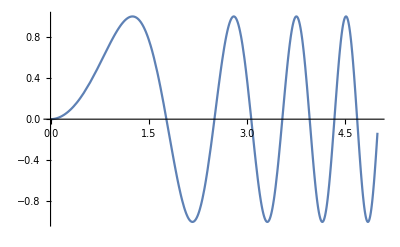

```mathematica
Plot[Sin[x^2], {x, 0, 5}]
```

```mathematica
Integrate[Sin[x^2], {x, 0, Infinity}]
```

(√(π/2))/2

Izračunajmo ločno dolžino krivulje y = x sin(x) na intervalu [0,a].

```mathematica
f[x_]:=x Sin[x]
```

```mathematica
g[x_]=Sqrt[1+(D[f[x], x])^2]
```

√(1+(x Cos[x]+Sin[x])^2)

```mathematica
ld[a_] = Integrate[g[x], {x, 0, a}]
```

∫_0^a √(1+(x Cos[x]+Sin[x])^2)ⅆx

Mathematica tega integrala ne zna izračunati za splošen a. Lahko pa integriramo numerično za dano vrednost, na primer a=3/2.

```mathematica
ld[a_] := NIntegrate[g[x], {x, 0, a}];
ld[3/2]
```

2.17561

Narišimo grafa funkcij f(x) in ld(x).

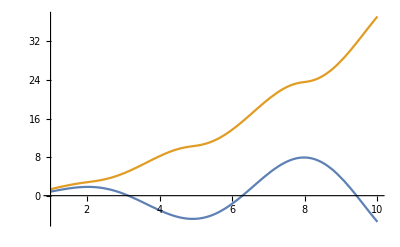

```mathematica
Plot[{f[x], ld[x]}, {x, 1, 10}]
```

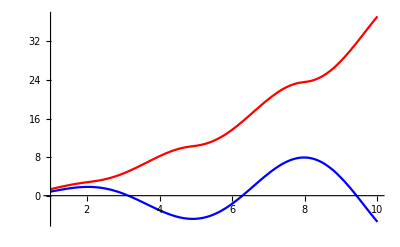

```mathematica
Plot[{f[x], ld[x]}, {x, 1, 10}, 
  PlotStyle -> {RGBColor[0, 0, 1], RGBColor[1, 0, 0]}]
```